# Computations for an American Mathematical Monthly Article

```mathematica
Clear["Global`*"]
```

## Trapezoidal Rule

```mathematica
traprule[f_,N_]:=((f[0]+f[1])/2+Sum[f[i/N],{i,1,N-1}])/N
```

```mathematica
simprule[f_,Nov2_]:=(f[0]+f[1]+4Sum[f[(i-1/2)/Nov2],{i,1,Nov2}]+2Sum[f[i/Nov2],{i,1,Nov2-1}])/(6Nov2)
```

```mathematica
xf[x_]:=x-1/2
ixf=Integrate[xf[x],{x,0,1}]
errxf=Simplify[ixf-{traprule[xf,N],simprule[xf,N/2]}]
```

0

{0,0}

```mathematica
x2f[x_]:=(x-1/2)^2
ix2f=Integrate[x2f[x],{x,0,1}]
errx2f=Simplify[ix2f-{traprule[x2f,N],simprule[x2f,N/2]}]
errhatx2f=Simplify[traprule[x2f,N]-traprule[x2f,N/2],Assumptions -> N/2∈Integers]
```

1/12

{-1/(6 N^2),0}

-1/(2 N^2)

```mathematica
x3f[x_]:=(x-1/2)^3
ix3f=Integrate[x3f[x],{x,0,1}]
errx3f=Simplify[ix3f-{traprule[x3f,N],simprule[x3f,N/2]}]
```

0

{0,0}

```mathematica
x4f[x_]:=(x-1/2)^4
ix4f=Integrate[x4f[x],{x,0,1}]
errx4f=Simplify[ix4f-{traprule[x4f,N],simprule[x4f,N/2]}]
```

1/80

{(2-5 N^2)/(60 N^4),-2/(15 N^4)}

```mathematica
x1absf[x_]:=Abs[x-1/2]
ix1absf=Integrate[x1absf[x],{x,0,1}]
errx1absf={Simplify[ix1absf-{traprule[x1absf,N],simprule[x1absf,N/2]},Assumptions -> N/4∈Integers],Simplify[ix1absf-{traprule[x1absf,N],simprule[x1absf,N/2]},Assumptions -> (N+2)/4∈Integers]}
```

1/4

{{0,0},{0,1/(3 N^2)}}

```mathematica
x3absf[x_]:=(Abs[x-1/2])^3
ix3absf=Integrate[x3absf[x],{x,0,1}]
errx3absf={Simplify[ix3absf-{traprule[x3absf,N],simprule[x3absf,N/2]},Assumptions -> N/4∈Integers],Simplify[ix3absf-{traprule[x3absf,N],simprule[x3absf,N/2]},Assumptions -> (N+2)/4∈Integers]}
errhatx3absf={Simplify[Simplify[traprule[x3absf,4M]-traprule[x3absf,2M],Assumptions -> M∈Integers]/. M -> N/4],Simplify[Simplify[traprule[x3absf,4M+2]-traprule[x3absf,2M+1],Assumptions -> M∈Integers]/. M -> (N-2)/4]}
```

1/32

{{-1/(8 N^2),0},{-1/(8 N^2),-1/(6 N^4)}}

{-3/(8 N^2),(4-3 N^2)/(8 N^4)}

## Gaussian Distribution Example

```mathematica
phi[x_]=Exp[-x^2/2]/Sqrt[2*Pi]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
dphi[x_]=D[phi[x],x]
```

-(ⅇ^(-x^2/2) x)/(√(2 π))

```mathematica
Maximize[{dphi[x],x≥0,x≤1},x]
```

{0,{x→0}}

```mathematica
Minimize[{dphi[x],x≥0,x≤1},x]
```

{-1/(√(2 ⅇ π)),{x→1}}

## Spiky Function Example

### Spiky Function and Its Derivatives

```mathematica
fgeneralhump[x_,a_,b_]= 30 (b-x)^2 (x-a)^2/(b-a)^4
```

(30 (b-x)^2 (-a+x)^2)/(-a+b)^4

```mathematica
Integrate[fgeneralhump[x,a,b],{x,a,b}]
```

-a+b

```mathematica
fhump[x_]=Simplify[1+30BernoulliB[4,x]]
```

30 (-1+x)^2 x^2

```mathematica
Integrate[fhump[x],{x,0,1}]
```

1

```mathematica
Simplify[fhump[1/2]] (*Maximum value of fhump*)
```

15/8

```mathematica
fhump[0]
```

0

```mathematica
dfhump[x_]=Factor[D[fhump[x],x]]
```

60 (-1+x) x (-1+2 x)

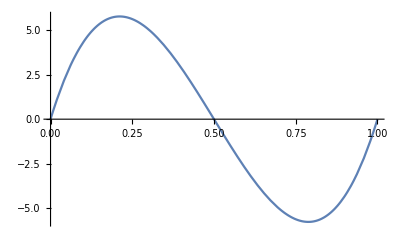

```mathematica
Plot[dfhump[x],{x,0,1}]
```

```mathematica
ddfhump[x_]=Factor[D[dfhump[x],x]]
```

60 (1-6 x+6 x^2)

```mathematica
dddfhump[x_]=Factor[D[ddfhump[x],x]]
```

360 (-1+2 x)

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfhump[x]==0,x]
```

{{x→1/6 (3-√3)},{x→1/6 (3+√3)}}

```mathematica
nodedx=Simplify[x/.noded]
```

{1/6 (3-√3),1/6 (3+√3)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,1/6 (3-√3),1/6 (3+√3),1}

```mathematica
nodedy=Simplify[dfhump[nodedx]]
```

{0,10/(√3),-10/(√3),0}

```mathematica
totvardfhump=Sum[Abs[Differences[nodedy]][[i]],{i,1,3}]
```

40/(√3)

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodeddx={0,1/2,1}
```

{0,1/2,1}

```mathematica
nodeddy=Simplify[ddfhump[nodeddx]]
```

{60,-30,60}

```mathematica
totvarddfhump=Sum[Abs[Differences[nodeddy]][[i]],{i,1,2}]
```

180

### Total Variation of Third Derivative of Fluky Function

```mathematica
nodedddx={0,1}
```

{0,1}

```mathematica
nodedddy=Simplify[dddfhump[nodedddx]]
```

{-360,360}

```mathematica
totvarddfhump=Sum[Abs[Differences[nodedddy]][[i]],{i,1,1}]
```

720

## Fluky Function Example

### Fluky Function and Its Derivatives

```mathematica
foolB[x_,M_]=Simplify[1-(15/2)*M^2*(BernoulliB[2,x]+M^2 BernoulliB[4,x])]
```

1-15/2 M^2 (1/6-x+x^2+M^2 (-1/30+x^2-2 x^3+x^4))

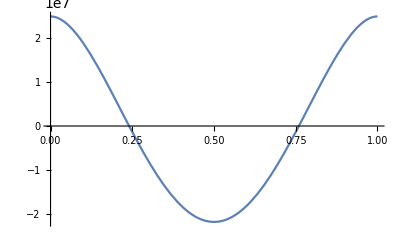

```mathematica
Plot [foolB[x,100],{x,0,1}]
```

```mathematica
Integrate[foolB[x,M],{x,0,1}]
```

1

```mathematica
fB2[x_]=BernoulliB[2,x]
Simplify[traprule[fB2,N]]
```

1/6-x+x^2

1/(6 N^2)

```mathematica
fB4[x_]=BernoulliB[4,x]
Simplify[traprule[fB4,N]]
```

-1/30+x^2-2 x^3+x^4

-1/(30 N^4)

```mathematica
f4[x_]=x^4
Simplify[traprule[f4,N]]
```

x^4

1/30 (6-1/N^4+10/N^2)

```mathematica
ffoolB[x_]=Simplify[foolB[x,M]]
```

1-15/2 M^2 (1/6-x+x^2+M^2 (-1/30+x^2-2 x^3+x^4))

```mathematica
ffoolBalt[x_]=1/4 (4-5 M^2+M^4) + (15/2) M^2 x(1-x)(1-M^2x(1-x))
```

1/4 (4-5 M^2+M^4)+15/2 M^2 (1-x) x (1-M^2 (1-x) x)

```mathematica
Simplify[ffoolB[x]-ffoolBalt[x]]
```

0

```mathematica
Simplify[foolB[x,M]-ffoolBalt[x]]
```

0

```mathematica
Simplify[traprule[ffoolB,N]]
```

1/4 (4+M^4/N^4-(5 M^2)/N^2)

```mathematica
Simplify[traprule[ffoolB,N/2]]
```

1+(4 M^4)/N^4-(5 M^2)/N^2

```mathematica
errfool=Simplify[Abs[Integrate[foolB[x,M],{x,0,1}]-Simplify[traprule[ffoolB,N]]],M>0 && N>0]
```

Abs[M^4-5 M^2 N^2]/(4 N^4)

```mathematica
errest=Simplify[Abs[Simplify[traprule[ffoolB,N]]-Simplify[traprule[ffoolB,N/2]]],M>0 && N>0]
```

(15 Abs[M^4-M^2 N^2])/(4 N^4)

```mathematica
Simplify[traprule[ffoolB,N/4]]
```

1+(64 M^4)/N^4-(20 M^2)/N^2

```mathematica
dfoolB[x_,N_]=Simplify[D[foolB[x,N],x]]
```

-15/2 N^2 (-1+2 x) (1+2 N^2 (-1+x) x)

```mathematica
ddfoolB[x_,N_]=Simplify[D[dfoolB[x,N],x]]
```

-15 (N^2+N^4 (1-6 x+6 x^2))

```mathematica
dddfoolB[x_,N]=Simplify[D[ddfoolB[x,N],x]]
```

-90 N^4 (-1+2 x)

```mathematica
ddddfoolB[x_,N]=D[dddfoolB[x,N],x]
```

-180 N^4

### Total Variation of Fluky Function

```mathematica
node=Solve[dfoolB[x,N]==0,x]
```

{{x→1/2},{x→(N^2-√(-2 N^2+N^4))/(2 N^2)},{x→(N^2+√(-2 N^2+N^4))/(2 N^2)}}

```mathematica
nodex=x/.node
```

{1/2,(N^2-√(-2 N^2+N^4))/(2 N^2),(N^2+√(-2 N^2+N^4))/(2 N^2)}

```mathematica
nodex={0,nodex[[2]],nodex[[1]],nodex[[3]],1}
```

{0,(N^2-√(-2 N^2+N^4))/(2 N^2),1/2,(N^2+√(-2 N^2+N^4))/(2 N^2),1}

```mathematica
nodey=Simplify[foolB[nodex,N]]
```

{1/4 (4-5 N^2+N^4),1/8 (23-10 N^2+2 N^4),1+(5 N^2)/8-(7 N^4)/32,1/8 (23-10 N^2+2 N^4),1/4 (4-5 N^2+N^4)}

```mathematica
absdify=Simplify[Abs[Differences[nodey]]]
```

{15/8,15/32 Abs[-2+N^2]^2,15/32 Abs[-2+N^2]^2,15/8}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,4}],Assumptions -> N≥ 2]]
```

15/2-(15 N^2)/4+(15 N^4)/16

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfoolB[x,N]==0,x]
```

{{x→(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2)},{x→(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2)}}

```mathematica
nodedx=x/.noded
```

{(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2),(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,(3 N^2-√3 √(-2 N^2+N^4))/(6 N^2),(3 N^2+√3 √(-2 N^2+N^4))/(6 N^2),1}

```mathematica
nodedy=Simplify[dfoolB[nodedx,N]]
```

{(15 N^2)/2,-(5 (N^2 (-2+N^2))^(3/2))/(2 √3 N^2),(5 (N^2 (-2+N^2))^(3/2))/(2 √3 N^2),-(15 N^2)/2}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> N≥4]
```

{5/6 N (9 N+√3 (-2+N^2)^(3/2)),(5 N (-2+N^2)^(3/2))/(√3),5/6 N (9 N+√3 (-2+N^2)^(3/2))}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> N≥4]
```

5/3 N (9 N+2 √3 (-2+N^2)^(3/2))

```mathematica
conetaufool=Simplify[totvardfool/totvarfool]
```

(16 N (9 N+2 √3 (-2+N^2)^(3/2)))/(9 (8-4 N^2+N^4))

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodedd=Solve[dddfoolB[x,N]==0,x]
```

{{x→1/2}}

```mathematica
nodeddx=x/.nodedd
```

{1/2}

```mathematica
nodeddx={0,nodeddx[[1]],1}
```

{0,1/2,1}

```mathematica
nodeddy=Simplify[ddfoolB[nodeddx,N]]
```

{-15 (N^2+N^4),15/2 N^2 (-2+N^2),-15 (N^2+N^4)}

```mathematica
absdifddy=Simplify[Abs[Differences[nodeddy]]]
```

{(45 Abs[N]^4)/2,(45 Abs[N]^4)/2}

```mathematica
totvarddfool=Simplify[Sum[absdifddy[[i]],{i,1,2}],Assumptions -> N∈Integers]
```

45 N^4

### A Slightly Different Function

```mathematica
badfoolB2[x_,N_]=15*N^2BernoulliB[2,x]
```

15 N^2 (1/6-x+x^2)

```mathematica
Integrate[badfoolB2[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB2[i/N,N],{i,0,N-1}]/N
```

5/2

```mathematica
trapNov2=Sum[badfoolB2[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

10

```mathematica
errhat=(trapN - trapNov2)/3
```

-5/2

```mathematica
badfoolB4[x_,N_]=15*N^4BernoulliB[4,x]
```

15 N^4 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[badfoolB4[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB4[i/N,N],{i,0,N-1}]/N
```

-1/2

```mathematica
trapNov2=Sum[badfoolB4[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

-8

```mathematica
errhat=(trapN - trapNov2)/3
```

5/2

## Big, Not Fluky Function Example

### Fluky Function and Its Derivatives

```mathematica
fbig[x_,M_]=1+(15/2)*M^4*(1/30 -(x*(1-x))^2)
```

1+15/2 M^4 (1/30-(1-x)^2 x^2)

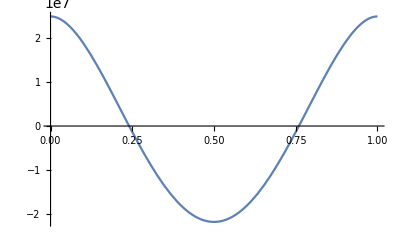

```mathematica
Plot [fbig[x,100],{x,0,1}]
```

```mathematica
Integrate[fbig[x,M],{x,0,1}]
```

1

```mathematica
ffbig[x_]=Simplify[fbig[x,M]]
```

1+15/2 M^4 (1/30-(-1+x)^2 x^2)

```mathematica
trapruleN=Simplify[traprule[ffbig,N]]
```

1+M^4/(4 N^4)

```mathematica
trapruleNov2 =Simplify[traprule[ffbig,N/2]]
```

1+(4 M^4)/N^4

```mathematica
error=Simplify[Abs[Integrate[fbig[x,N],{x,0,1}]-traprule[ffbig,N]],M>0 && N>0]
```

M^4/(4 N^4)

```mathematica
errest=Simplify[Abs[(trapruleN-trapruleNov2)],M>0 && N>0]/3
```

(5 M^4)/(4 N^4)

```mathematica
dfbig[x_,M_]=Simplify[D[fbig[x,M],x]]
```

-15 M^4 x (1-3 x+2 x^2)

```mathematica
ddfbig[x_,M_]=Simplify[D[dfbig[x,M],x]]
```

-15 M^4 (1-6 x+6 x^2)

```mathematica
dddfbig[x_,M]=Simplify[D[ddfbig[x,M],x]]
```

-90 M^4 (-1+2 x)

```mathematica
ddddfbig[x_,M]=D[dddfbig[x,M],x]
```

-180 M^4

### Total Variation of Big Function

```mathematica
node=Solve[dfbig[x,M]==0,x]
```

{{x→0},{x→1/2},{x→1}}

```mathematica
nodex=x/.node
```

{0,1/2,1}

```mathematica
nodey=Simplify[fbig[nodex,M]]
```

{1/4 (4+M^4),1-(7 M^4)/32,1/4 (4+M^4)}

```mathematica
absdify=Simplify[Abs[Differences[nodey]],M>0]
```

{(15 M^4)/32,(15 M^4)/32}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,2}],Assumptions -> M≥ 2]]
```

(15 M^4)/16

### Total Variation of First Derivative of Big Function

```mathematica
noded=Solve[ddfbig[x,M]==0,x]
```

{{x→1/6 (3-√3)},{x→1/6 (3+√3)}}

```mathematica
nodedx=x/.noded
```

{1/6 (3-√3),1/6 (3+√3)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,1/6 (3-√3),1/6 (3+√3),1}

```mathematica
nodedy=Simplify[dfbig[nodedx,M]]
```

{0,-(5 M^4)/(2 √3),(5 M^4)/(2 √3),0}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> M≥4]
```

{(5 M^4)/(2 √3),(5 M^4)/(√3),(5 M^4)/(2 √3)}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> M≥4]
```

(10 M^4)/(√3)

## Alternative Fluky Function Example

### Fluky Function and Its Derivatives

```mathematica
foolB[x_,N_]=Simplify[1-60*N^2*(BernoulliB[2,x/2]+4N^2 BernoulliB[4,x/2])]
```

1-5 N^2 (2-6 x+3 x^2)+N^4 (8-60 x^2+60 x^3-15 x^4)

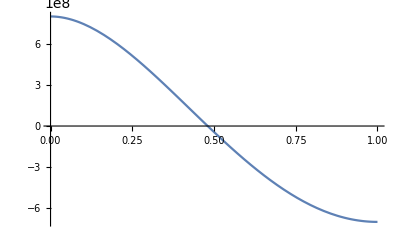

```mathematica
Plot [foolB[x,100],{x,0,1}]
```

```mathematica
Integrate[foolB[x,N],{x,0,1}]
```

1

```mathematica
fB2[x_]=BernoulliB[2,x/2]
```

1/6-x/2+x^2/4

```mathematica
Simplify[traprule[fB2,N]]
```

1/(24 N^2)

```mathematica
Simplify[traprule[fB2,N/2]]
```

1/(6 N^2)

```mathematica
fB4[x_]=BernoulliB[4,x/2]
```

-1/30+x^2/4-x^3/4+x^4/16

```mathematica
Simplify[traprule[fB4,N]]
```

-1/(480 N^4)

```mathematica
Simplify[traprule[fB4,N/2]]
```

-1/(30 N^4)

```mathematica
Simplify[traprule[fB2,N]]+4N^2 Simplify[traprule[fB4,N]]
```

1/(30 N^2)

```mathematica
ffoolB[x_]=foolB[x,N]
```

1-5 N^2 (2-6 x+3 x^2)+N^4 (8-60 x^2+60 x^3-15 x^4)

```mathematica
BernoulliB[4,x]
```

-1/30+x^2-2 x^3+x^4

```mathematica
Simplify[traprule[ffoolB,N]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/2]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/4]]
```

89

```mathematica
dfoolB[x_,N]=Simplify[-120*N^2*(BernoulliB[1,x]+4N^2(BernoulliB[3,x/2]-1))]
```

-60 N^2 (-1+2 x+N^2 (-8+2 x-3 x^2+x^3))

```mathematica
ddfoolB[x_,N]=Simplify[-30*N^2*(1+24 N^2BernoulliB[2,x/2])]
```

-30 N^2 (1+2 N^2 (2-6 x+3 x^2))

```mathematica
dddfoolB[x_,N]=Simplify[-720* N^4BernoulliB[1,x/2]]
```

-360 N^4 (-1+x)

```mathematica
ddddfoolB[x_,N]=-360* N^4
```

-360 N^4

### Total Variation of Fluky Function

```mathematica
node=Solve[dfoolB[x,N]==0,x]
```

{{x→1+((2/3)^(1/3) (-2 N^2+N^4))/(N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))+((-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))/(2^(1/3) 3^(2/3) N^2)},{x→1-((1+ⅈ √3) (-2 N^2+N^4))/(2^(2/3) 3^(1/3) N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3)},{x→1-((1-ⅈ √3) (-2 N^2+N^4))/(2^(2/3) 3^(1/3) N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3)}}

```mathematica
nodex=x/.node
```

{1+((2/3)^(1/3) (-2 N^2+N^4))/(N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))+((-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))/(2^(1/3) 3^(2/3) N^2),1-((1+ⅈ √3) (-2 N^2+N^4))/(2^(2/3) 3^(1/3) N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3),1-((1-ⅈ √3) (-2 N^2+N^4))/(2^(2/3) 3^(1/3) N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3)}

```mathematica
nodex={0,nodex[[2]],nodex[[1]],nodex[[3]],1}
```

{0,1-((1+ⅈ √3) (-2 N^2+N^4))/(2^(2/3) 3^(1/3) N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3),1+((2/3)^(1/3) (-2 N^2+N^4))/(N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))+((-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))/(2^(1/3) 3^(2/3) N^2),1-((1-ⅈ √3) (-2 N^2+N^4))/(2^(2/3) 3^(1/3) N^2 (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+72 N^6+√3 √(32 N^6-21 N^8-408 N^10+1724 N^12))^(1/3),1}

```mathematica
nodey=Simplify[foolB[nodex,N]]
```

{1-10 N^2+8 N^4,1-5 N^2 (2-6 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+1/(2 2^(1/3) 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+3 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+1/(2 2^(1/3) 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^2)+N^4 (8-60 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+1/(2 2^(1/3) 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^2+60 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+1/(2 2^(1/3) 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^3-15 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+1/(2 2^(1/3) 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^4),1-(5 (24 2^(2/3) 3^(1/3) N^4-24 2^(2/3) 3^(1/3) N^6+6 2^(2/3) 3^(1/3) N^8-24 N^2 (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+6 N^4 (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(4/3)))/(6 N^2 (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3))+N^4 (8-60 (1+((2/3)^(1/3) (-2+N^2))/(-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3)+1/(2^(1/3) 3^(2/3) N^2)(-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^2+60 (1+((2/3)^(1/3) (-2+N^2))/(-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3)+1/(2^(1/3) 3^(2/3) N^2)(-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^3-15 (1+((2/3)^(1/3) (-2+N^2))/(-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3)+1/(2^(1/3) 3^(2/3) N^2)(-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^4),1-5 N^2 (2-6 (1+(ⅈ (ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+3 (1+(ⅈ (ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^2)+N^4 (8-60 (1+(ⅈ (ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^2+60 (1+(ⅈ (ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^3-15 (1+(ⅈ (ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))-1/(2 2^(1/3) 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))^4),1+5 N^2-7 N^4}

```mathematica
absdify=Simplify[Abs[Differences[nodey]]]
```

{Abs[N^2 (10-8 N^2-5 (2-6 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+1/(2 2^(1/3) 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+3 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+(ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))/(2 2^(1/3) 3^(2/3) N^2))^2)+N^2 (8-60 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+(ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))/(2 2^(1/3) 3^(2/3) N^2))^2+60 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+(ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))/(2 2^(1/3) 3^(2/3) N^2))^3-15 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))+(ⅈ (ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(1/3))/(2 2^(1/3) 3^(2/3) N^2))^4))],1/(2 2^(2/3))5 3^(1/6) Abs[(-15612 (ⅈ+√3) N^10-6900 (ⅈ+√3) N^12-3 2^(1/3) 3^(1/6) (-ⅈ+√3) √(N^6 (32-21 N^2-408 N^4+1724 N^6)) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+3 N^4 (-32 ⅈ-32 √3-228 √(N^6 (32-21 N^2-408 N^4+1724 N^6))-76 ⅈ √3 √(N^6 (32-21 N^2-408 N^4+1724 N^6))+9 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)-3 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3))+14 N^8 (306 ⅈ+306 √3+123 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)-41 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3))+6 ⅈ N^6 (-37+37 ⅈ √3+48 ⅈ √(N^6 (32-21 N^2-408 N^4+1724 N^6))-16 √3 √(N^6 (32-21 N^2-408 N^4+1724 N^6))+69 ⅈ 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+23 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3))+2 N^2 (45 √(N^6 (32-21 N^2-408 N^4+1724 N^6))+15 ⅈ √3 √(N^6 (32-21 N^2-408 N^4+1724 N^6))-12 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+4 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)-12 ⅈ 2^(1/3) 3^(1/6) √(N^6 (32-21 N^2-408 N^4+1724 N^6)) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+12 2^(1/3) 3^(2/3) √(N^6 (32-21 N^2-408 N^4+1724 N^6)) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)))/(-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(4/3)],1/(2 2^(2/3))5 3^(1/6) Abs[(-15612 (-ⅈ+√3) N^10-6900 (-ⅈ+√3) N^12-3 2^(1/3) 3^(1/6) (ⅈ+√3) √(N^6 (32-21 N^2-408 N^4+1724 N^6)) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+3 N^4 (32 ⅈ-32 √3-228 √(N^6 (32-21 N^2-408 N^4+1724 N^6))+76 ⅈ √3 √(N^6 (32-21 N^2-408 N^4+1724 N^6))+9 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+3 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3))+14 N^8 (-306 ⅈ+306 √3+123 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+41 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3))-6 ⅈ N^6 (-37-37 ⅈ √3-48 ⅈ √(N^6 (32-21 N^2-408 N^4+1724 N^6))-16 √3 √(N^6 (32-21 N^2-408 N^4+1724 N^6))-69 ⅈ 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+23 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3))+2 N^2 (45 √(N^6 (32-21 N^2-408 N^4+1724 N^6))-15 ⅈ √3 √(N^6 (32-21 N^2-408 N^4+1724 N^6))-12 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)-4 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+12 ⅈ 2^(1/3) 3^(1/6) √(N^6 (32-21 N^2-408 N^4+1724 N^6)) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+12 2^(1/3) 3^(2/3) √(N^6 (32-21 N^2-408 N^4+1724 N^6)) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)))/(-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(4/3)],1/(288 6^(1/3))5 Abs[((4 3^(1/3) (ⅈ+√3) N^2-2 3^(1/3) (ⅈ+√3) N^4+2^(1/3) (-ⅈ+√3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3))^2 (24 2^(2/3) 3^(1/3) N^4+24 ⅈ 2^(2/3) 3^(5/6) N^4-24 2^(2/3) 3^(1/3) N^6-24 ⅈ 2^(2/3) 3^(5/6) N^6+6 2^(2/3) 3^(1/3) N^8+6 ⅈ 2^(2/3) 3^(5/6) N^8+12 N^2 (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)+48 N^4 (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(2/3)-3 ⅈ 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(4/3)+2^(1/3) 3^(2/3) (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(4/3)))/(N^4 (-9 N^4+72 N^6+√3 √(N^6 (32-21 N^2-408 N^4+1724 N^6)))^(4/3))]}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,4}],Assumptions -> N≥ 2]]
```

1/(288 6^(1/3))5 Abs[((4 3^(1/3) (ⅈ+√3) N^2-2 3^(1/3) (ⅈ+√3) N^4+2^(1/3) (-ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))^2 (24 2^(2/3) 3^(1/3) N^4+24 ⅈ 2^(2/3) 3^(5/6) N^4-24 2^(2/3) 3^(1/3) N^6-24 ⅈ 2^(2/3) 3^(5/6) N^6+6 2^(2/3) 3^(1/3) N^8+6 ⅈ 2^(2/3) 3^(5/6) N^8+12 N^4 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+48 N^6 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)-3 ⅈ 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(4/3)+2^(1/3) 3^(2/3) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(4/3)))/(N^8 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(4/3))]+(5 3^(1/6) Abs[-15612 (ⅈ+√3) N^10-6900 (ⅈ+√3) N^12-3 2^(1/3) 3^(1/6) (-ⅈ+√3) N^5 √(32-21 N^2-408 N^4+1724 N^6) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+3 N^4 (-32 (ⅈ+√3)-76 ⅈ (-3 ⅈ+√3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+3 2^(1/3) 3^(1/6) (3-ⅈ √3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))+6 ⅈ N^6 (37 ⅈ (ⅈ+√3)-16 (-3 ⅈ+√3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+23 2^(1/3) 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))+2 N^2 (15 (3+ⅈ √3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+4 ⅈ 2^(1/3) 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+12 2^(1/3) 3^(1/6) (-ⅈ+√3) N^5 √(32-21 N^2-408 N^4+1724 N^6) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))+14 N^8 (306 ⅈ+306 √3+123 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(2/3)-41 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(2/3))])/(2 2^(2/3) N^4 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(4/3))+(5 3^(1/6) Abs[15612 (-ⅈ+√3) N^10+6900 (-ⅈ+√3) N^12+3 2^(1/3) 3^(1/6) (ⅈ+√3) N^5 √(32-21 N^2-408 N^4+1724 N^6) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)-3 N^4 (-32 (-ⅈ+√3)+76 ⅈ (3 ⅈ+√3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+3 2^(1/3) 3^(1/6) (3+ⅈ √3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))+6 ⅈ N^6 (-37-37 ⅈ √3-16 (3 ⅈ+√3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+23 2^(1/3) 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))-2 N^2 (15 (3-ⅈ √3) N^3 √(32-21 N^2-408 N^4+1724 N^6)-4 ⅈ 2^(1/3) 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+12 2^(1/3) 3^(1/6) (ⅈ+√3) N^5 √(32-21 N^2-408 N^4+1724 N^6) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))-14 N^8 (-306 ⅈ+306 √3+123 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+41 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(2/3))])/(2 2^(2/3) N^4 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(4/3))+N^2 Abs[10-8 N^2-5 (2-6 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+1/(2 2^(1/3) 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+3 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+1/(2 2^(1/3) 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))^2)+N^2 (8-60 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+1/(2 2^(1/3) 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))^2+60 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+1/(2 2^(1/3) 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))^3-15 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+1/(2 2^(1/3) 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))^4)]

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfoolB[x,N]==0,x]
```

{{x→(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2)},{x→(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2)}}

```mathematica
nodedx=x/.noded
```

{(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2),(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2),(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2),1}

```mathematica
nodedy=Simplify[dfoolB[nodedx,N]]
```

{60 N^2 (1+8 N^2),-5/3 (-288 N^4-11 √6 √(N^2 (-1+2 N^2))+4 N^2 (9+√6 √(N^2 (-1+2 N^2)))),5/3 (288 N^4-11 √6 √(N^2 (-1+2 N^2))+4 N^2 (-9+√6 √(N^2 (-1+2 N^2)))),60 N^2 (-1+8 N^2)}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> N≥2]
```

{5/3 N (72 N-11 √(-6+12 N^2)+4 N^2 √(-6+12 N^2)),10/3 N (-11+4 N^2) √(-6+12 N^2),5/3 N (-11+4 N^2) √(-6+12 N^2)}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> N≥2]
```

20/3 N (18 N-11 √(-6+12 N^2)+4 N^2 √(-6+12 N^2))

```mathematica
conetaufool=Simplify[totvardfool/totvarfool]
```

(20 N (18 N-11 √(-6+12 N^2)+4 N^2 √(-6+12 N^2)))/(3 (1/(288 6^(1/3))5 Abs[((4 3^(1/3) (ⅈ+√3) N^2-2 3^(1/3) (ⅈ+√3) N^4+2^(1/3) (-ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))^2 (24 2^(2/3) 3^(1/3) N^4+24 ⅈ 2^(2/3) 3^(5/6) N^4-24 2^(2/3) 3^(1/3) N^6-24 ⅈ 2^(2/3) 3^(5/6) N^6+6 2^(2/3) 3^(1/3) N^8+6 ⅈ 2^(2/3) 3^(5/6) N^8+12 N^4 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+48 N^6 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)-3 ⅈ 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(4/3)+2^(1/3) 3^(2/3) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(4/3)))/(N^8 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(4/3))]+(5 2^(1/3) 3^(1/6) Abs[-15612 (ⅈ+√3) N^10-6900 (ⅈ+√3) N^12-3 2^(1/3) 3^(1/6) (-ⅈ+√3) N^5 √(32-21 N^2-408 N^4+1724 N^6) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+3 N^4 (-32 (ⅈ+√3)-76 ⅈ (-3 ⅈ+√3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+3 2^(1/3) 3^(1/6) (3-ⅈ √3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))+6 ⅈ N^6 (37 ⅈ (ⅈ+√3)-16 (-3 ⅈ+√3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+23 2^(1/3) 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))+2 N^2 (15 (3+ⅈ √3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+4 ⅈ 2^(1/3) 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+12 2^(1/3) 3^(1/6) (-ⅈ+√3) N^5 √(32-21 N^2-408 N^4+1724 N^6) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))+14 N^8 (306 ⅈ+306 √3+123 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(2/3)-41 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(2/3))]+5 2^(1/3) 3^(1/6) Abs[15612 (-ⅈ+√3) N^10+6900 (-ⅈ+√3) N^12+3 2^(1/3) 3^(1/6) (ⅈ+√3) N^5 √(32-21 N^2-408 N^4+1724 N^6) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)-3 N^4 (-32 (-ⅈ+√3)+76 ⅈ (3 ⅈ+√3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+3 2^(1/3) 3^(1/6) (3+ⅈ √3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))+6 ⅈ N^6 (-37-37 ⅈ √3-16 (3 ⅈ+√3) N^3 √(32-21 N^2-408 N^4+1724 N^6)+23 2^(1/3) 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))-2 N^2 (15 (3-ⅈ √3) N^3 √(32-21 N^2-408 N^4+1724 N^6)-4 ⅈ 2^(1/3) 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+12 2^(1/3) 3^(1/6) (ⅈ+√3) N^5 √(32-21 N^2-408 N^4+1724 N^6) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(2/3))-14 N^8 (-306 ⅈ+306 √3+123 2^(1/3) 3^(1/6) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(2/3)+41 ⅈ 2^(1/3) 3^(2/3) (-9 N^4+72 N^6+N^3 √(96-63 N^2-1224 N^4+5172 N^6))^(2/3))]+4 N^6 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(4/3) Abs[10-8 N^2-5 (2-6 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+(ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))/(2 2^(1/3) 3^(2/3) N))+3 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+(ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))/(2 2^(1/3) 3^(2/3) N))^2)+N^2 (8-60 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+(ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))/(2 2^(1/3) 3^(2/3) N))^2+60 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+(ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))/(2 2^(1/3) 3^(2/3) N))^3-15 (1-(ⅈ (-ⅈ+√3) (-2+N^2))/(2^(2/3) 3^(1/3) N (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))+(ⅈ (ⅈ+√3) (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(1/3))/(2 2^(1/3) 3^(2/3) N))^4)])/(4 N^4 (-9 N+72 N^3+√(96-63 N^2-1224 N^4+5172 N^6))^(4/3))))

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodedd=Solve[dddfoolB[x,N]==0,x]
```

{{x→1}}

```mathematica
nodeddx=x/.nodedd
```

{1}

```mathematica
nodeddx={0,nodeddx[[1]],1}
```

{0,1,1}

```mathematica
nodeddy=Simplify[ddfoolB[nodeddx,N]]
```

{-30 N^2 (1+4 N^2),30 N^2 (-1+2 N^2),30 N^2 (-1+2 N^2)}

```mathematica
absdifddy=Simplify[Abs[Differences[nodeddy]]]
```

{180 Abs[N]^4,0}

```mathematica
totvarddfool=Simplify[Sum[absdifddy[[i]],{i,1,2}],Assumptions -> N∈Integers]
```

180 N^4

### A Slightly Different Function

```mathematica
badfoolB2[x_,N_]=15*N^2BernoulliB[2,x]
```

15 N^2 (1/6-x+x^2)

```mathematica
Integrate[badfoolB2[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB2[i/N,N],{i,0,N-1}]/N
```

5/2

```mathematica
trapNov2=Sum[badfoolB2[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

10

```mathematica
errhat=(trapN - trapNov2)/3
```

-5/2

```mathematica
badfoolB4[x_,N_]=15*N^4BernoulliB[4,x]
```

15 N^4 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[badfoolB4[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB4[i/N,N],{i,0,N-1}]/N
```

-1/2

```mathematica
trapNov2=Sum[badfoolB4[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

-8

```mathematica
errhat=(trapN - trapNov2)/3
```

5/2

## Another Alternative Fluky Function Example

### Fluky Function and Its Derivatives

```mathematica
foolB[x_,N_]=Simplify[1-15*N^2*(BernoulliB[2,x]+N^2 (16BernoulliB[4,x/2]-BernoulliB[1,x]))]
```

1-5/2 N^2 (1-6 x+6 x^2)+N^4 (1/2+15 x-60 x^2+60 x^3-15 x^4)

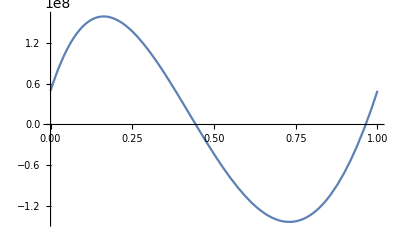

```mathematica
Plot [foolB[x,100],{x,0,1}]
```

```mathematica
Integrate[foolB[x,N],{x,0,1}]
```

1

```mathematica
ffoolB[x_]=foolB[x,N]
```

1-5/2 N^2 (1-6 x+6 x^2)+N^4 (1/2+15 x-60 x^2+60 x^3-15 x^4)

```mathematica
BernoulliB[4,x]
```

-1/30+x^2-2 x^3+x^4

```mathematica
Simplify[traprule[ffoolB,N]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/2]]
```

-1

```mathematica
Simplify[traprule[ffoolB,N/4]]
```

89

```mathematica
dfoolB[x_,N]=Simplify[-30*N^2*(BernoulliB[1,x]+16N^2(BernoulliB[3,x/2]-1))]
```

-30 N^2 (-1/2+x+2 N^2 (-8+2 x-3 x^2+x^3))

```mathematica
ddfoolB[x_,N]=Simplify[-30*N^2*(1+24 N^2BernoulliB[2,x/2])]
```

-30 N^2 (1+2 N^2 (2-6 x+3 x^2))

```mathematica
dddfoolB[x_,N]=Simplify[-720* N^4BernoulliB[1,x/2]]
```

-360 N^4 (-1+x)

```mathematica
ddddfoolB[x_,N]=-360* N^4
```

-360 N^4

### Total Variation of Fluky Function

```mathematica
node=Solve[dfoolB[x,N]==0,x]
```

{{x→1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2)},{x→1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)},{x→1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}}

```mathematica
nodex=x/.node
```

{1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}

```mathematica
nodex={0,nodex[[2]],nodex[[1]],nodex[[3]],1}
```

{0,1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1}

```mathematica
nodey=Simplify[foolB[nodex,N]]
```

{1/2 (2-5 N^2+N^4),1/2 (2-5 N^2 (1-6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)+2 N^4 (1/2+15 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))-60 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2+60 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^3-15 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^4)),1/2 (2-5 N^2 (1-6 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))+6 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))^2)+2 N^4 (1/2+15 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))-60 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))^2+60 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))^3-15 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))^4)),1/2 (2-5 N^2 (1-6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)+2 N^4 (1/2+15 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))-60 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2+60 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^3-15 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^4)),1/2 (2-5 N^2+N^4)}

```mathematica
absdify=Simplify[Abs[Differences[nodey]]]
```

{Abs[1/2 (-2+5 N^2-N^4)+1/2 (2-5 N^2 (1-6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)+2 N^4 (1/2+15 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))-60 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2+60 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^3-15 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^4))],5/16 3^(1/6) Abs[(144816 (ⅈ+√3) N^10-234624 (ⅈ+√3) N^12+9 3^(1/6) (-ⅈ+√3) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+3 N^4 (8 ⅈ+8 √3+480 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+160 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-51 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+17 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+12 N^6 (11 ⅈ+11 √3-204 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-68 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+165 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-55 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+32 N^8 (-441 ⅈ-441 √3+753 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-251 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+4 N^2 (-27 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-9 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+3 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-21 ⅈ 3^(1/6) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+21 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(4/3)],5/16 3^(1/6) Abs[(144816 (-ⅈ+√3) N^10-234624 (-ⅈ+√3) N^12+9 3^(1/6) (ⅈ+√3) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+3 N^4 (-8 ⅈ+8 √3+480 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-160 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))-51 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)-17 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+12 N^6 (-11 ⅈ+11 √3-204 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+68 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+165 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+55 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+32 N^8 (441 ⅈ-441 √3+753 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+251 ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))+4 N^2 (-27 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+9 ⅈ √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+3 3^(1/6) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+21 ⅈ 3^(1/6) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+ⅈ (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)+21 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3)))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(4/3)],Abs[1/2 (2-5 N^2+N^4)+1/2 (-2+5 N^2 (1-6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)-2 N^4 (1/2+15 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))-60 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2+60 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^3-15 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^4))]}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,4}],Assumptions -> N≥ 2]]
```

(5 3^(1/6) Abs[144816 (ⅈ+√3) N^10-234624 (ⅈ+√3) N^12+9 3^(1/6) (-ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+3 N^4 (8 (ⅈ+√3)+160 (3+ⅈ √3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+17 ⅈ 3^(1/6) (3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+4 N^2 (-9 ⅈ (-3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+3^(1/6) (3-ⅈ √3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+21 3^(1/6) (-ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+32 N^8 (-441 ⅈ-441 √3+753 3^(1/6) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3)-251 ⅈ 3^(2/3) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+12 N^6 (-68 ⅈ (-3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+11 (ⅈ+√3+5 3^(1/6) (3-ⅈ √3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)))])/(16 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(4/3))+(5 3^(1/6) Abs[144816 (-ⅈ+√3) N^10-234624 (-ⅈ+√3) N^12+9 3^(1/6) (ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+3 N^4 (8 (-ⅈ+√3)+160 (3-ⅈ √3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)-17 ⅈ 3^(1/6) (-3 ⅈ+√3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+4 N^2 (9 ⅈ (3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+3^(1/6) (3+ⅈ √3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+21 3^(1/6) (ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+32 N^8 (441 ⅈ-441 √3+753 3^(1/6) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3)+251 ⅈ 3^(2/3) (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+12 N^6 (68 ⅈ (3 ⅈ+√3) N^3 √(8-21 N^2-1632 N^4+27584 N^6)+11 (-ⅈ+√3+5 3^(1/6) (3+ⅈ √3) N^2 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3)))])/(16 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(4/3))+Abs[1/2 (2-5 N^2+N^4)+1/2 (-2+5 N^2 (1-6 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+6 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2)-2 N^4 (1/2+15 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-60 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2+60 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^3-15 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^4))]+Abs[1/2 (-2+5 N^2-N^4)+1/2 (2-5 N^2 (1-6 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+6 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2)+2 N^4 (1/2+15 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-60 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2+60 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^3-15 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^4))]

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfoolB[x,N]==0,x]
```

{{x→(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2)},{x→(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2)}}

```mathematica
nodedx=x/.noded
```

{(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2),(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2),(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2),1}

```mathematica
nodedy=Simplify[dfoolB[nodedx,N]]
```

{15 N^2 (1+32 N^2),-5/3 (-288 N^4-2 √6 √(N^2 (-1+2 N^2))+N^2 (9+4 √6 √(N^2 (-1+2 N^2)))),5/3 (288 N^4-2 √6 √(N^2 (-1+2 N^2))+N^2 (-9+4 √6 √(N^2 (-1+2 N^2)))),15 N^2 (-1+32 N^2)}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> N≥2]
```

{10/3 N (9 N-√(-6+12 N^2)+2 N^2 √(-6+12 N^2)),20 √(2/3) N (-1+2 N^2)^(3/2),10 √(2/3) N (-1+2 N^2)^(3/2)}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> N≥2]
```

10/3 N (9 N-4 √(-6+12 N^2)+8 N^2 √(-6+12 N^2))

```mathematica
conetaufool=Simplify[totvardfool/totvarfool]
```

$Aborted

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodedd=Solve[dddfoolB[x,N]==0,x]
```

{{x→1}}

```mathematica
nodeddx=x/.nodedd
```

{1}

```mathematica
nodeddx={0,nodeddx[[1]],1}
```

{0,1,1}

```mathematica
nodeddy=Simplify[ddfoolB[nodeddx,N]]
```

{-30 N^2 (1+4 N^2),30 N^2 (-1+2 N^2),30 N^2 (-1+2 N^2)}

```mathematica
absdifddy=Simplify[Abs[Differences[nodeddy]]]
```

{180 Abs[N]^4,0}

```mathematica
totvarddfool=Simplify[Sum[absdifddy[[i]],{i,1,2}],Assumptions -> N∈Integers]
```

180 N^4

### A Slightly Different Function

```mathematica
badfoolB2[x_,N_]=15*N^2BernoulliB[2,x]
```

15 N^2 (1/6-x+x^2)

```mathematica
Integrate[badfoolB2[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB2[i/N,N],{i,0,N-1}]/N
```

5/2

```mathematica
trapNov2=Sum[badfoolB2[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

10

```mathematica
errhat=(trapN - trapNov2)/3
```

-5/2

```mathematica
badfoolB4[x_,N_]=15*N^4BernoulliB[4,x]
```

15 N^4 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[badfoolB4[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB4[i/N,N],{i,0,N-1}]/N
```

-1/2

```mathematica
trapNov2=Sum[badfoolB4[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

-8

```mathematica
errhat=(trapN - trapNov2)/3
```

5/2

## Still Another Alternative Fluky Function Example

### Checking Pieces

```mathematica
nonzeroerrpc[x_,N_]=Simplify[(3N^2/2)*((-4+3N^2)((x-1/2)^2-1/12) -4 N^2 ((Abs[x-1/2])^3-1/32))]
```

3/2 N^2 (1/6 (-4+3 N^2) (1-6 x+6 x^2)-4 N^2 (-1/32+Abs[-1/2+x]^3))

```mathematica
Integrate[nonzeroerrpc[x,N],{x,0,1}]
```

0

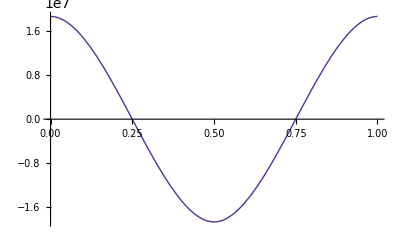

```mathematica
Plot [nonzeroerrpc[x,100],{x,0,1}]
```

```mathematica
nzerrN[x_]=Simplify[nonzeroerrpc[x,N]]
```

3/2 N^2 (1/6 (-4+3 N^2) (1-6 x+6 x^2)-4 N^2 (-1/32+Abs[-1/2+x]^3))

```mathematica
errnonzeroerrpc=Simplify[Simplify[Integrate[nzerrN[x],{x,0,1}]-traprule[nzerrN,2M+1],Assumptions -> M∈Integers]/. M -> (N-2)/4]
```

1

```mathematica
errhatnonzeroerrpc=Simplify[Simplify[traprule[nzerrN,4M+2]-traprule[nzerrN,2M+1],Assumptions -> M∈Integers]/. M -> (N-2)/4, Assumptions -> N > 2]
```

0

### Fluky Function and Its Derivatives

```mathematica
foolB[x_,N_]=1+2nonzeroerrpc[x,N]
```

1+3 N^2 (1/6 (-4+3 N^2) (1-6 x+6 x^2)-4 N^2 (-1/32+Abs[-1/2+x]^3))

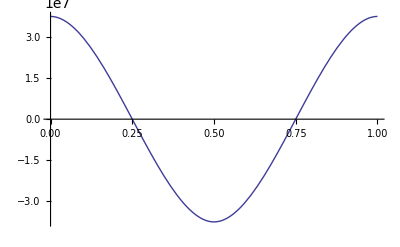

```mathematica
Plot [foolB[x,100],{x,0,1}]
```

```mathematica
Integrate[foolB[x,N],{x,0,1}]
```

1

```mathematica
ffoolB[x_]=foolB[x,N]
```

1+3 N^2 (1/6 (-4+3 N^2) (1-6 x+6 x^2)-4 N^2 (-1/32+Abs[-1/2+x]^3))

```mathematica
BernoulliB[4,x]
```

-1/30+x^2-2 x^3+x^4

```mathematica
Simplify[traprule[ffoolB,N]]
```

1/8 (-8+12 N^2+12 N^3+3 N^4-24 N (2+3 N+N^2) Ceiling[N/2]+24 (2+6 N+3 N^2) Ceiling[N/2]^2-96 (1+N) Ceiling[N/2]^3+48 Ceiling[N/2]^4)

```mathematica
Simplify[traprule[ffoolB,N/2]]
```

1/8 (-56+48 N^2+24 N^3+3 N^4-48 N (8+6 N+N^2) Ceiling[N/4]+96 (8+12 N+3 N^2) Ceiling[N/4]^2-768 (2+N) Ceiling[N/4]^3+768 Ceiling[N/4]^4)

```mathematica
Simplify[traprule[ffoolB,N/4]]
```

1/8 (-248+192 N^2+48 N^3+3 N^4-96 N (32+12 N+N^2) Ceiling[N/8]+384 (32+24 N+3 N^2) Ceiling[N/8]^2-6144 (4+N) Ceiling[N/8]^3+12288 Ceiling[N/8]^4)

```mathematica
dfoolB[x_,N]=Simplify[-30*N^2*(BernoulliB[1,x]+16N^2(BernoulliB[3,x/2]-1))]
```

-30 N^2 (-1/2+x+2 N^2 (-8+2 x-3 x^2+x^3))

```mathematica
ddfoolB[x_,N]=Simplify[-30*N^2*(1+24 N^2BernoulliB[2,x/2])]
```

-30 N^2 (1+2 N^2 (2-6 x+3 x^2))

```mathematica
dddfoolB[x_,N]=Simplify[-720* N^4BernoulliB[1,x/2]]
```

-360 N^4 (-1+x)

```mathematica
ddddfoolB[x_,N]=-360* N^4
```

-360 N^4

### Total Variation of Fluky Function

```mathematica
node=Solve[dfoolB[x,N]==0,x]
```

{{x→1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2)},{x→1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)},{x→1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}}

```mathematica
nodex=x/.node
```

{1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3)}

```mathematica
nodex={0,nodex[[2]],nodex[[1]],nodex[[3]],1}
```

{0,1-((1+ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1-ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1+(-N^2+2 N^4)/(3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))+((-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))/(2 3^(2/3) N^2),1-((1-ⅈ √3) (-N^2+2 N^4))/(2 3^(1/3) N^2 (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3))-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(8 N^6-21 N^8-1632 N^10+27584 N^12))^(1/3),1}

```mathematica
nodey=Simplify[foolB[nodex,N]]
```

{1-2 N^2+(3 N^4)/8,1+3 N^2 (1/6 (-4+3 N^2) (1-6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)-1/432 N^2 (-54+Abs[6-(2 ⅈ 3^(2/3) (-ⅈ+√3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+1/N^2 ⅈ (ⅈ+√3) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3)),1+3 N^2 (1/6 (-4+3 N^2) (1-6 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))+6 (1+1/(2 3^(2/3) N^2)(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(-1+2 N^2)/(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))^2)+1/8 N^2 (1-4/27 Abs[3+(2 3^(2/3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+1/N^2(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3)),1+3 N^2 (1/6 (-4+3 N^2) (1-6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)-1/432 N^2 (-54+Abs[6+(2 ⅈ 3^(2/3) (ⅈ+√3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-1/N^2 ⅈ (-ⅈ+√3) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3)),1-2 N^2+(3 N^4)/8}

```mathematica
absdify=Simplify[Abs[Differences[nodey]]]
```

{Abs[2 N^2-(3 N^4)/8+3 N^2 (1/6 (-4+3 N^2) (1-6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+6 (1+1/(4 3^(2/3) N^2)ⅈ (ⅈ+√3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)-1/432 N^2 (-54+Abs[6-(2 ⅈ 3^(2/3) (-ⅈ+√3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+1/N^2 ⅈ (ⅈ+√3) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3))],1/144 Abs[(18 3^(1/6) (-4+3 N^2) (592 3^(1/6) (3-ⅈ √3) N^8+6 3^(1/6) (-ⅈ+√3) N^2 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+(3+ⅈ √3) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+N^4 (12 3^(1/6)-4 ⅈ 3^(2/3)-21 ⅈ (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-21 √3 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))+2 N^6 (-51 3^(1/6)+17 ⅈ 3^(2/3)+156 ⅈ (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+156 √3 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))-8 N^6 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3) Abs[3+(2 3^(2/3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+1/N^2(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3+N^6 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3) Abs[6-(2 ⅈ 3^(2/3) (-ⅈ+√3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+1/N^2ⅈ (ⅈ+√3) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3)/(N^2 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))],1/144 Abs[(-18 3^(1/6) (-4+3 N^2) (592 3^(1/6) (3+ⅈ √3) N^8+6 3^(1/6) (ⅈ+√3) N^2 √(N^6 (8-21 N^2-1632 N^4+27584 N^6))+(3-ⅈ √3) √(N^6 (8-21 N^2-1632 N^4+27584 N^6)) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+N^4 (12 3^(1/6)+4 ⅈ 3^(2/3)+21 ⅈ (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-21 √3 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3))+2 N^6 (-51 3^(1/6)-17 ⅈ 3^(2/3)-156 ⅈ (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+156 √3 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+8 N^6 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3) Abs[3+(2 3^(2/3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+1/N^2(-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3-N^6 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3) Abs[6+(2 ⅈ 3^(2/3) (ⅈ+√3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-1/N^2ⅈ (-ⅈ+√3) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3)/(N^2 (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(2/3))],Abs[2 N^2-(3 N^4)/8+3 N^2 (1/6 (-4+3 N^2) (1-6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))+6 (1-1/(4 3^(2/3) N^2)(1+ⅈ √3) (-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)))^2)-1/432 N^2 (-54+Abs[6+(2 ⅈ 3^(2/3) (ⅈ+√3) (-1+2 N^2))/(-9 N^4+288 N^6+√3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)-1/N^2 ⅈ (-ⅈ+√3) (-27 N^4+864 N^6+3 √3 √(N^6 (8-21 N^2-1632 N^4+27584 N^6)))^(1/3)]^3))]}

```mathematica
totvarfool=Expand[Simplify[Sum[absdify[[i]],{i,1,4}],Assumptions -> N≥ 2]]
```

Abs[(8 N^5 (-2 3^(2/3)+4 3^(2/3) N^2+3 N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+3^(1/3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))^3)/(-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)-18 3^(1/6) (-4+3 N^2) (592 3^(1/6) (3+ⅈ √3) N^8+6 3^(1/6) (ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6)+(3-ⅈ √3) N^4 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+N^4 (4 3^(1/6) (3+ⅈ √3)-21 (-ⅈ+√3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+2 N^6 (-17 ⅈ 3^(1/6) (-3 ⅈ+√3)+156 (-ⅈ+√3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)))-N^6 (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3) Abs[6+(2 ⅈ 3^(2/3) (ⅈ+√3) (-1+2 N^2))/(N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/Nⅈ 3^(1/3) (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)]^3]/(144 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+Abs[2 N^2-(3 N^4)/8+3 N^2 (1/6 (-4+3 N^2) (1-6 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+6 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2)-1/432 N^2 (-54+Abs[6+(2 ⅈ 3^(2/3) (ⅈ+√3) (-1+2 N^2))/(N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/N ⅈ 3^(1/3) (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)]^3))]+Abs[-(8 N^5 (-2 3^(2/3)+4 3^(2/3) N^2+3 N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+3^(1/3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))^3)/(-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+18 3^(1/6) (-4+3 N^2) (592 3^(1/6) (3-ⅈ √3) N^8+6 3^(1/6) (-ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6)+(3+ⅈ √3) N^4 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+N^4 (4 3^(1/6) (3-ⅈ √3)-21 (ⅈ+√3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+2 N^6 (17 ⅈ 3^(1/6) (3 ⅈ+√3)+156 (ⅈ+√3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)))+N^6 (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3) Abs[6-(2 ⅈ 3^(2/3) (-ⅈ+√3) (-1+2 N^2))/(N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/Nⅈ 3^(1/3) (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)]^3]/(144 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+Abs[2 N^2-(3 N^4)/8+3 N^2 (1/6 (-4+3 N^2) (1-6 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+6 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2)-1/432 N^2 (-54+Abs[6-(2 ⅈ 3^(2/3) (-ⅈ+√3) (-1+2 N^2))/(N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/N ⅈ 3^(1/3) (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)]^3))]

### Total Variation of First Derivative of Fluky Function

```mathematica
noded=Solve[ddfoolB[x,N]==0,x]
```

{{x→(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2)},{x→(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2)}}

```mathematica
nodedx=x/.noded
```

{(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2),(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2)}

```mathematica
nodedx={0,nodedx[[1]],nodedx[[2]],1}
```

{0,(6 N^2-√6 √(-N^2+2 N^4))/(6 N^2),(6 N^2+√6 √(-N^2+2 N^4))/(6 N^2),1}

```mathematica
nodedy=Simplify[dfoolB[nodedx,N]]
```

{15 N^2 (1+32 N^2),-5/3 (-288 N^4-2 √6 √(N^2 (-1+2 N^2))+N^2 (9+4 √6 √(N^2 (-1+2 N^2)))),5/3 (288 N^4-2 √6 √(N^2 (-1+2 N^2))+N^2 (-9+4 √6 √(N^2 (-1+2 N^2)))),15 N^2 (-1+32 N^2)}

```mathematica
absdifdy=Simplify[Abs[Differences[nodedy]],Assumptions -> N≥2]
```

{10/3 N (9 N-√(-6+12 N^2)+2 N^2 √(-6+12 N^2)),20 √(2/3) N (-1+2 N^2)^(3/2),10 √(2/3) N (-1+2 N^2)^(3/2)}

```mathematica
totvardfool=Simplify[Sum[absdifdy[[i]],{i,1,3}],Assumptions -> N≥2]
```

10/3 N (9 N-4 √(-6+12 N^2)+8 N^2 √(-6+12 N^2))

```mathematica
conetaufool=Simplify[totvardfool/totvarfool]
```

(10 N (9 N-4 √(-6+12 N^2)+8 N^2 √(-6+12 N^2)))/(3 (Abs[(8 N^5 (-2 3^(2/3)+4 3^(2/3) N^2+3 N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+3^(1/3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))^3)/(-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)-18 3^(1/6) (-4+3 N^2) (592 3^(1/6) (3+ⅈ √3) N^8+6 3^(1/6) (ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6)+(3-ⅈ √3) N^4 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+N^4 (4 3^(1/6) (3+ⅈ √3)-21 (-ⅈ+√3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+2 N^6 (-17 ⅈ 3^(1/6) (-3 ⅈ+√3)+156 (-ⅈ+√3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)))-N^6 (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3) Abs[6+(2 ⅈ 3^(2/3) (ⅈ+√3) (-1+2 N^2))/(N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/Nⅈ 3^(1/3) (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)]^3]/(144 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+Abs[2 N^2-(3 N^4)/8+3 N^2 (1/6 (-4+3 N^2) (1-6 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+6 (1+(ⅈ (ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/(4 3^(2/3) N)ⅈ (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2)-1/432 N^2 (-54+Abs[6+(2 ⅈ 3^(2/3) (ⅈ+√3) (-1+2 N^2))/(N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))-1/Nⅈ 3^(1/3) (-ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)]^3))]+Abs[-(8 N^5 (-2 3^(2/3)+4 3^(2/3) N^2+3 N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+3^(1/3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))^3)/(-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+18 3^(1/6) (-4+3 N^2) (592 3^(1/6) (3-ⅈ √3) N^8+6 3^(1/6) (-ⅈ+√3) N^5 √(8-21 N^2-1632 N^4+27584 N^6)+(3+ⅈ √3) N^4 √(8-21 N^2-1632 N^4+27584 N^6) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)+N^4 (4 3^(1/6) (3-ⅈ √3)-21 (ⅈ+√3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+2 N^6 (17 ⅈ 3^(1/6) (3 ⅈ+√3)+156 (ⅈ+√3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)))+N^6 (-9 N^4+288 N^6+N^3 √(24-63 N^2-4896 N^4+82752 N^6))^(2/3) Abs[6-(2 ⅈ 3^(2/3) (-ⅈ+√3) (-1+2 N^2))/(N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/Nⅈ 3^(1/3) (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)]^3]/(144 N^4 (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(2/3))+Abs[2 N^2-(3 N^4)/8+3 N^2 (1/6 (-4+3 N^2) (1-6 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+6 (1-(ⅈ (-ⅈ+√3) (-1+2 N^2))/(2 3^(1/3) N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/(4 3^(2/3) N)ⅈ (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))^2)-1/432 N^2 (-54+Abs[6-(2 ⅈ 3^(2/3) (-ⅈ+√3) (-1+2 N^2))/(N (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3))+1/Nⅈ 3^(1/3) (ⅈ+√3) (-9 N+288 N^3+√(24-63 N^2-4896 N^4+82752 N^6))^(1/3)]^3))]))

### Total Variation of Second Derivative of Fluky Function

```mathematica
nodedd=Solve[dddfoolB[x,N]==0,x]
```

{{x→1}}

```mathematica
nodeddx=x/.nodedd
```

{1}

```mathematica
nodeddx={0,nodeddx[[1]],1}
```

{0,1,1}

```mathematica
nodeddy=Simplify[ddfoolB[nodeddx,N]]
```

{-30 N^2 (1+4 N^2),30 N^2 (-1+2 N^2),30 N^2 (-1+2 N^2)}

```mathematica
absdifddy=Simplify[Abs[Differences[nodeddy]]]
```

{180 Abs[N]^4,0}

```mathematica
totvarddfool=Simplify[Sum[absdifddy[[i]],{i,1,2}],Assumptions -> N∈Integers]
```

180 N^4

### A Slightly Different Function

```mathematica
badfoolB2[x_,N_]=15*N^2BernoulliB[2,x]
```

15 N^2 (1/6-x+x^2)

```mathematica
Integrate[badfoolB2[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB2[i/N,N],{i,0,N-1}]/N
```

5/2

```mathematica
trapNov2=Sum[badfoolB2[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

10

```mathematica
errhat=(trapN - trapNov2)/3
```

-5/2

```mathematica
badfoolB4[x_,N_]=15*N^4BernoulliB[4,x]
```

15 N^4 (-1/30+x^2-2 x^3+x^4)

```mathematica
Integrate[badfoolB4[x,N],{x,0,1}]
```

0

```mathematica
trapN=Sum[badfoolB4[i/N,N],{i,0,N-1}]/N
```

-1/2

```mathematica
trapNov2=Sum[badfoolB4[i/(N/2),N],{i,0,N/2-1}]/(N/2)
```

-8

```mathematica
errhat=(trapN - trapNov2)/3
```

5/2

## Bernoulli Polynomials

```mathematica
Factor[BernoulliB[3,x]]
```

1/2 (-1+x) x (-1+2 x)

```mathematica
Factor[D[BernoulliB[4,x],x]]
```

2 (-1+x) x (-1+2 x)

```mathematica
Factor[BernoulliB[5,x]]
```

1/6 (-1+x) x (-1+2 x) (-1-3 x+3 x^2)